```mathematica
(* based on Carl Bender's lecture series Mathemtical Physics *)
(* se Episode 3, https://www.youtube.com/watch?v=_Sm7SNlNUOI around 1:02:20 *)
(* and Episode 4, https://www.youtube.com/watch?v=VvqeJkT3uyo around 4:40*)
```

## Shanks Transformation

```mathematica
(* Shanks acceleration is for partial sums which oscillate around the limit *)
```

```mathematica
shanksFromList[e_]:=Module[{tmpTable,i,n},
If[Head[e≠List],Print["Input is not a list."];Return[e]; ];
tmpTable=Table[0,{n,1,Length[e]-2}];
For[i=1,i≤Length[tmpTable],i++,
n=i+1;
tmpTable[[i]]=(e[[n-1]]e[[n+1]]-e[[n]]^2)/(e[[n+1]]-2e[[n]]+e[[n-1]])
];
Return[tmpTable];
]
```

### Shanks Example

```mathematica
Log[2]//N
```

0.693147

```mathematica
nTerms=100;
```

{1.,0.5,0.833333,0.583333,0.783333,0.616667,0.759524,0.634524,0.745635,0.645635,0.736544,0.653211,0.730134,0.658705,0.725372,0.662872,0.721695,0.66614,0.718771,0.668771,0.71639,0.670936,0.714414,0.672747,0.712747,0.674286,0.711323,0.675609,0.710091,0.676758,0.709016,0.677766,0.708069,0.678657,0.707229,0.679451,0.706478,0.680162,0.705803,0.680803,0.705194,0.681384,0.70464,0.681913,0.704135,0.682396,0.703672,0.682839,0.703247,0.683247,0.702855,0.683624,0.702492,0.683974,0.702155,0.684298,0.701842,0.684601,0.70155,0.684883,0.701277,0.685148,0.701021,0.685396,0.70078,0.685629,0.700554,0.685848,0.700341,0.686055,0.70014,0.686251,0.69995,0.686436,0.699769,0.686612,0.699599,0.686778,0.699436,0.686936,0.699282,0.687087,0.699135,0.68723,0.698995,0.687367,0.698861,0.687498,0.698734,0.687622,0.698611,0.687742,0.698495,0.687856,0.698383,0.687966,0.698275,0.688071,0.698172,0.688172}

{0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693146,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693146,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693148,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693148,0.693147,0.693147,0.693148,0.693147,0.693147,0.693147,0.693147,0.693146,0.693148,0.693147,0.693148,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693147,0.693146,0.693156,0.693147,0.693147,0.693148}

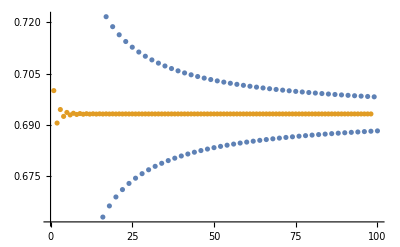

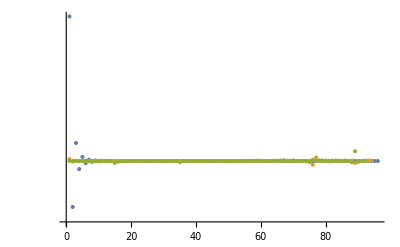

```mathematica
partialSumLog2[n_]:=Sum[(-1)^(m-1)/m,{m,1,n}]
tableLog2=Table[partialSumLog2[n],{n,1,nTerms}]//N
shanks1Log2=tableLog2//shanksFromList;
shanks2Log2=shanks1Log2//shanksFromList;
shanks3Log2=shanks2Log2//shanksFromList;
shanks4Log2=shanks3Log2//shanksFromList

plotLog2ConvergenceFirst=ListPlot[{tableLog2,shanks1Log2}] (* efficacy of a single Shanks transformation *)
plotLog2ConvergenceSecond=ListLogPlot[{shanks2Log2,shanks3Log2,shanks4Log2},PlotRange->All] (* efficacy of the iterated Shanks transformations *)
```

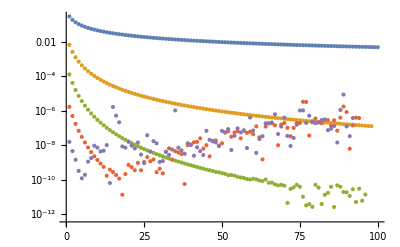

```mathematica
residualsLog2Partial = Abs@(tableLog2-Log[2]);
residualsLog2Shanks1 = Abs@(shanks1Log2-Log[2]);
residualsLog2Shanks2 = Abs@(shanks2Log2-Log[2]);
residualsLog2Shanks3 = Abs@(shanks3Log2-Log[2]);
residualsLog2Shanks4 = Abs@(shanks4Log2-Log[2]);

plotLog2Difference=ListLogPlot[{residualsLog2Partial,residualsLog2Shanks1,residualsLog2Shanks2,residualsLog2Shanks3,residualsLog2Shanks4}]
```

## Richardson Transformation

```mathematica
(* Richardson acceleration is for partial sums which monotonically approach the limit *)
```

```mathematica
richardsonNFromList[N_,e_]:=Module[{tmpTable,i},
If[Head[e≠List],Print["Input is not a list."];Return[e]; ];
tmpTable=Table[0,{n,1,Length[e]-N}];
For[i=1,i≤Length[tmpTable],i++,
tmpTable[[i]]=Sum[(-1)^(n-N)Binomial[N,n](i+n)^N*e[[i+n]]/Factorial[N],{n,0,N}];
];
Return[tmpTable];
]
```

```mathematica
(* the lowest Richardson is N=2 . Writing this out explicity so it can be compared to the higher N cases*)
richardsonFromList[e_]:=Module[{tmpTable,i},
If[Head[e≠List],Print["Input is not a list."];Return[e]; ];
tmpTable=Table[0,{n,1,Length[e]-2}];
For[i=1,i≤Length[tmpTable],i++,
tmpTable[[i]]=((i+2)^2e[[i+2]]-2(i+1)^2e[[i+1]]+i^2e[[i]])/2;
];
Return[tmpTable];
]
```

### Richardson Example: Zeta[2] = Pi^2/6

```mathematica
nTerms=100;
```

#### Iterated First Richardsons

```mathematica
N[Pi^2/6,10]
```

1.644934067

1.644934046

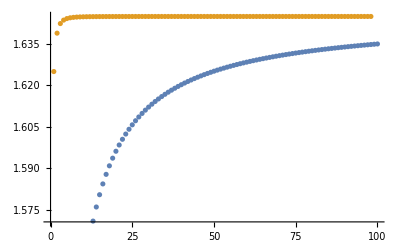

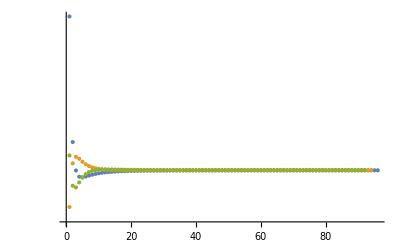

```mathematica
(* iterated Richardsons *)
partialSumZeta2[n_]:=Sum[1/m^2,{m,1,n}]
tableZeta2=Table[partialSumZeta2[n],{n,1,nTerms}];
richardson1Zeta2=tableZeta2//richardsonFromList;
richardson2Zeta2=richardson1Zeta2//richardsonFromList;
richardson3Zeta2=richardson2Zeta2//richardsonFromList;
richardson4Zeta2=richardson3Zeta2//richardsonFromList;

N[richardson4Zeta2//Last,10]

plotZeta2ConvergenceFirst=ListPlot[{tableZeta2,richardson1Zeta2}] (* efficacy of a single richardson transformation *)
plotZeta2ConvergenceSecond=ListLogPlot[{richardson2Zeta2,richardson3Zeta2,richardson4Zeta2},PlotRange->All] (* efficacy of the iterated Shanks transformations *)
```

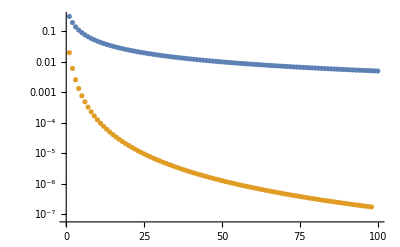

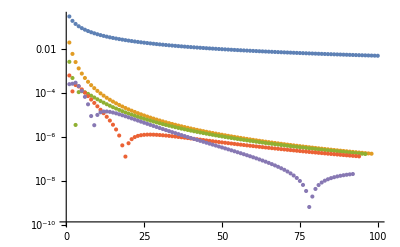

```mathematica
residualsZeta2Partial = Abs@(tableLog2-Zeta[2]);
residualsZeta2Richardson1 = Abs@(richardson1Zeta2-Zeta[2]);
residualsZeta2Richardson2 = Abs@(richardson2Zeta2-Zeta[2]);
residualsZeta2Richardson3 = Abs@(richardson3Zeta2-Zeta[2]);
residualsZeta2Richardson4 = Abs@(richardson4Zeta2-Zeta[2]);

plotLog2Difference=ListLogPlot[{residualsLog2Partial,residualsZeta2Richardson1}]

plotLog2Difference=ListLogPlot[{residualsLog2Partial,residualsZeta2Richardson1,residualsZeta2Richardson2,residualsZeta2Richardson3,residualsZeta2Richardson4}]
```

#### Iterated Second Richardsons

```mathematica
N[Pi^2/6,10]
```

1.644934067

```mathematica
richardson4FromList[e_]:=richardsonNFromList[4,e]
```

1.644934067

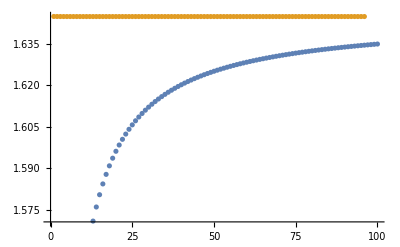

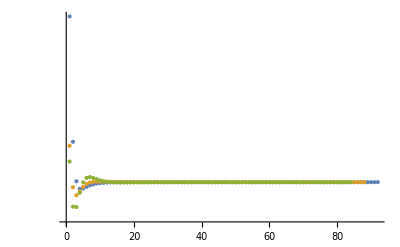

```mathematica
(* iterated Richardsons *)
partialSumZeta2[n_]:=Sum[1/m^2,{m,1,n}]
tableZeta2=Table[partialSumZeta2[n],{n,1,nTerms}];
richardson1Zeta2=tableZeta2//richardson4FromList;
richardson2Zeta2=richardson1Zeta2//richardson4FromList;
richardson3Zeta2=richardson2Zeta2//richardson4FromList;
richardson4Zeta2=richardson3Zeta2//richardson4FromList;

N[richardson4Zeta2//Last,10]

plotZeta2ConvergenceFirst=ListPlot[{tableZeta2,richardson1Zeta2}] (* efficacy of a single richardson transformation *)
plotZeta2ConvergenceSecond=ListLogPlot[{richardson2Zeta2,richardson3Zeta2,richardson4Zeta2},PlotRange->All] (* efficacy of the iterated Shanks transformations *)
```

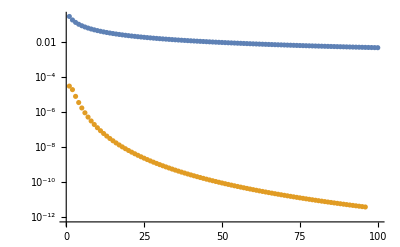

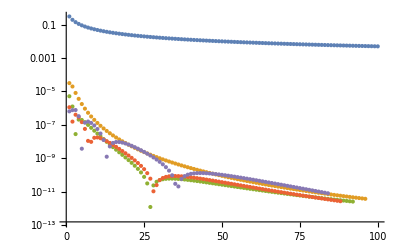

```mathematica
residualsZeta2Partial = Abs@(tableLog2-Zeta[2]);
residualsZeta2Richardson1 = Abs@(richardson1Zeta2-Zeta[2]);
residualsZeta2Richardson2 = Abs@(richardson2Zeta2-Zeta[2]);
residualsZeta2Richardson3 = Abs@(richardson3Zeta2-Zeta[2]);
residualsZeta2Richardson4 = Abs@(richardson4Zeta2-Zeta[2]);

plotLog2Difference=ListLogPlot[{residualsLog2Partial,residualsZeta2Richardson1}]

plotLog2Difference=ListLogPlot[{residualsLog2Partial,residualsZeta2Richardson1,residualsZeta2Richardson2,residualsZeta2Richardson3,residualsZeta2Richardson4}]
```

#### Nth Richardsons

```mathematica
N[Pi^2/6,10]
```

1.644934067

1.644934067

-Graphics-

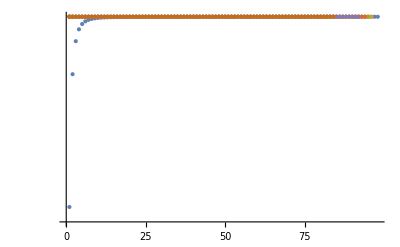

```mathematica
(* higher order Richardsons *)
partialSumZeta2[n_]:=Sum[1/m^2,{m,1,n}]
tableZeta2=Table[partialSumZeta2[n],{n,1,nTerms}];
richardson2Zeta2=richardsonNFromList[2,tableZeta2];
richardson4Zeta2=richardsonNFromList[4,tableZeta2];
richardson5Zeta2=richardsonNFromList[5,tableZeta2]; (* odd Rochardsons work too *)
richardson6Zeta2=richardsonNFromList[6,tableZeta2];
richardson8Zeta2=richardsonNFromList[8,tableZeta2];
richardson16Zeta2=richardsonNFromList[16,tableZeta2];

N[richardson16Zeta2//Last,10]

plotZeta2ConvergenceFirst=ListPlot[{tableZeta2,richardson2Zeta2}] (* efficacy of a single richardson transformation *)
plotZeta2ConvergenceSecond=ListLogPlot[{richardson2Zeta2,richardson4Zeta2,richardson5Zeta2,richardson6Zeta2,richardson8Zeta2,richardson16Zeta2},PlotRange->All] (* efficacy of the iterated Shanks transformations *)
```

-Graphics-

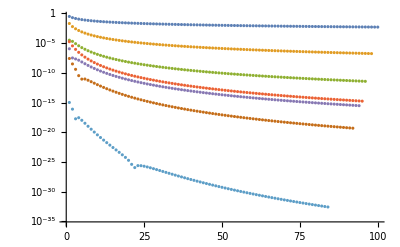

```mathematica
residualsZeta2Partial = Abs@(tableLog2-Zeta[2]);
residualsZeta2Richardson2 = Abs@(richardson2Zeta2-Zeta[2]);
residualsZeta2Richardson4 = Abs@(richardson4Zeta2-Zeta[2]);
residualsZeta2Richardson5 = Abs@(richardson5Zeta2-Zeta[2]);
residualsZeta2Richardson6 = Abs@(richardson6Zeta2-Zeta[2]);
residualsZeta2Richardson8 = Abs@(richardson8Zeta2-Zeta[2]);
residualsZeta2Richardson16 = Abs@(richardson16Zeta2-Zeta[2]);

plotLog2Difference=ListLogPlot[{residualsLog2Partial,residualsZeta2Richardson2}]

plotLog2Difference=ListLogPlot[{residualsLog2Partial,residualsZeta2Richardson2,residualsZeta2Richardson4,residualsZeta2Richardson5,residualsZeta2Richardson6,residualsZeta2Richardson8,residualsZeta2Richardson16}]
```

## Asymptotic Expansions and Non-Convergent Series

```mathematica
(* see Carl Bender episode 6 https://www.youtube.com/watch?v=nWKYrpKn3-0 *)

(* Pade approximants, Shanks, and coupled Robertsons*)
```

```mathematica
padeUpper[z_,N_]:=PadeApproximant[ g[z,2*N],{z,0,{N,N}}]
padeLower[z_,N_]:=PadeApproximant[g[z,2*N+1],{z,0,{N,N+1}}]
padeMain[z_,N_]:=If[Mod[N,2]==1,padeUpper[z,(N-1)/2],padeLower[z,(N-2)/2]]
```

### Quartic Gaussians

```mathematica
G[z_]:=NIntegrate[Exp[-x^2-z*x^4],{x,-Infinity,Infinity}]
```

```mathematica
(* let's say we're interested in G[z] at z=zstar = 13 *)
zstar=1;
G[zstar]
```

1.36843

```mathematica
(* the function G[z] gives an asymptotic series in z *)
a[n_]:=NIntegrate[SeriesCoefficient[Exp[-x^2-epsilon*x^4],{epsilon,0,n}],{x,-Infinity,Infinity}]
```

1.77245

1.77245-1.32934 z

5.81586 z^2-1.32934 z+1.77245

-47.9809 z^3+5.81586 z^2-1.32934 z+1.77245

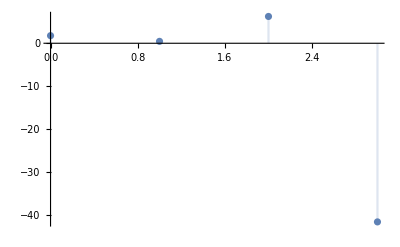

```mathematica
(* the first few partial sums gives *)

g0[z]=a[0]
g1[z]=a[0]+a[1]*z
g2[z]=a[0]+a[1]*z+a[2]*z^2/.epsilon->z
g3[z]=a[0]+a[1]*z+a[2]*z^2+a[3]*z^3/.epsilon->z

g[z_,n_]:=Sum[ a[m]*z^m ,{m,0,n}]

(* clearly getting worse as you include higher order terms, zero radius of convergence for the Taylor series *)
DiscretePlot[g[z,n]/.z->zstar,{n,0,3},PlotRange->All]
```

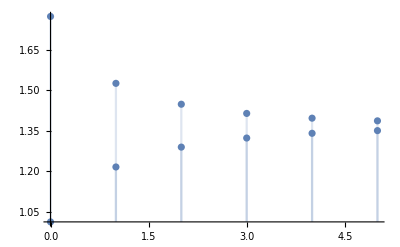

```mathematica
DiscretePlot[{padeUpper[z,n],padeLower[z,n]}/.z->zstar,{n,0,5},PlotRange->All]
```

{1.33343,1.34179,1.35149,1.35844,1.36296}

{1.40371,1.39569,1.38568,1.37851,1.37385}

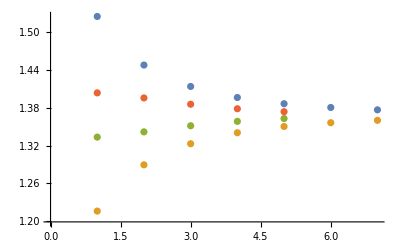

```mathematica
(* the padeUpper monotonically decrease towards G[zstar], while padeLower monotonically increases towards G[zstar] *)

(* try Richardson on each *)
nTerms=7;

tableUpper=Table[ padeUpper[z,n]/.z->zstar,{n,1,nTerms}];
richardson2Upper = richardsonNFromList[2, tableUpper ];

N[richardson2Upper,10]

tableLower=Table[ padeLower[z,n]/.z->zstar,{n,1,nTerms}];
richardson2Lower= richardsonNFromList[2, tableLower ];

N[richardson2Lower,10]

ListPlot[{tableUpper,tableLower,richardson2Upper,richardson2Lower}]
(* the 4th richardson doesn't behave very well though *)
```

```mathematica
richardson2Upper
richardson2Lower
```

{1.33343,1.34179,1.35149,1.35844,1.36296}

{1.40371,1.39569,1.38568,1.37851,1.37385}

1.36937

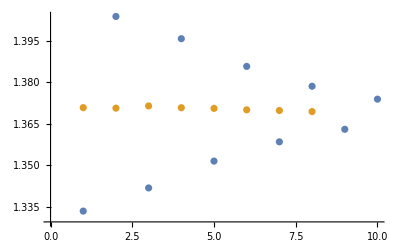

```mathematica
(* try Shanks on the Richardsons *)

interleavedRichardsons=Table[If[Mod[n,2]==1,richardson2Upper[[(n+1)/2]],richardson2Lower[[(n)/2]] ],{n,1,(nTerms-2)*2}];
shankedRichardson=interleavedRichardsons//shanksFromList;

N[shankedRichardson//Last,10]

ListPlot[{interleavedRichardsons,shankedRichardson}]
```

```mathematica
G[zstar]
```

1.36843

## ToDo:

```mathematica
(* the Pade can be written as b0/( 1+b1*x / (1+b2*x / (1+b3*x / ... ))) so if each subsequent pade in the sequence only changes the final row from bn=0 to bn =/= 0, the Shanks of 3 consecutive Pade entires might have a nice closed form *)
```